# Fig 6: Temporal Autocorrelation

### Import density calculations, and define data

```mathematica
densityALL=Get[savedir<>"densityALL"];
```

```mathematica
allNactual=Map[Length,allints,{3}];
totalinteractions=Total[Flatten[#]]&/@allNactual;
integrated=Map[integrateprob[#,1]&,densityALL,{3}];  (* here, using a value of 1, because the distance is one frame between each density. calculation. *)
getTotalIntegrated[allintegrated_]:=Table[Total@Flatten[allintegrated[[col]]],{col,Length@colnames}];
total=getTotalIntegrated[integrated];
normdensityAll=(densityALL*totalinteractions)/total;
```

### Data structure with start, end, interaction time list

```mathematica
allSEints=Table[
{
If[Length[alltrajinterpolated[[col,group,ant]]]==0,{},{alltrajinterpolated[[col,group,ant,1,1]],alltrajinterpolated[[col,group,ant,-1,1]]}],
allints[[col,group,ant,;;,1]]
}
,{col,4},{group,5},{ant,Length[alltrajinterpolated[[col,group]]]}];
```

### Define a filter time and get lists of interactions

```mathematica
filtertime=4; (* in seconds *)

(* keeps interactions within time range defined by filter time *)
sel[seint_,dt_]:=Select[seint[[2]],seint[[1,1]]+filtertime/dt≤ #≤ seint[[1,2]]-filtertime/dt&]; 
intlist[seint_,dt_]:=Module[{selected,full},  (* returns an interaction list, discarding the focus point at t=0 *)
selected=sel[seint,dt];
full=seint[[2]];
If[Length[selected]==0,{},
Select[dt (Complement[full,{#}]-#),Abs[#]≤filtertime&]&/@selected
]
];
allintlist=Table[Map[intlist[#,alldtused[[col]]]&,allSEints[[col]],{2}],{col,4}];
```

### Use interaction times to trigger density averages

```mathematica
npavg=Table[
If[Length[allSEints[[col,group,ant,1]]]==0,{},
Table[
Take[normdensityAll[[col,group,ant]]/alldtused[[col]],{selpos-Round[filtertime/alldtused[[col]]],selpos+Round[filtertime/alldtused[[col]]]}]
,{selpos,sel[allSEints[[col,group,ant]],alldtused[[col]]]-allSEints[[col,group,ant,1,1]]+1}]
]
,{col,4},{group,5},{ant,Length[normdensityAll[[col,group]]]}];
```

### Equivalent rates for Poisson process - define for each colony observation

```mathematica
totaltimes=Map[Total[Select[#,#≠Infinity&]]&,alltimes,{2}];
equivrates=(Total[Flatten@#]&/@allNactual)/(Total/@totaltimes)
```

{0.532989,0.320107,0.670413,0.573225}

### Mean and standard error of density calculations

```mathematica
percolavg=Map[Mean[Flatten[#,2]]&,npavg];
percolse=Map[StandardDeviation[Flatten[#,2]]/Sqrt[Length[Flatten[#,2]]]&,npavg];
```

### Create plots

```mathematica
numbins=31;  (* use 31 for 4 sec *)

(* smoothing for display *)
errorbarnumsmooth=8;
meannumsmooth=5;
alldtmultwholecol=2 filtertime/(alldtused numbins);
alldtwholecol=alldtused alldtmultwholecol;
allbinswholecol={-filtertime,filtertime,#}&/@(alldtwholecol );
coldatahists=Table[
Show[
Histogram[Flatten[allintlist[[col]]],allbinswholecol[[col]],#2/(Length[Flatten[allintlist[[col]],2]]alldtwholecol[[col]])&,PlotRange->{{-filtertime,filtertime},{0,Automatic}},AxesOrigin->0,Frame->True,FrameTicks->{Automatic,Automatic},PlotLabel->Style["Colony "<>ToString[col],16],ChartStyle->Automatic]
],{col,4}];
(* plots for average, and standard deviation *)

plotnvavg=Table[{Range[-filtertime,filtertime,alldtused[[col]]],percolavg[[col]]}ᵀ,{col,4}];
colavgplots=
Table[ListPlot[(gaussianMovingAverage[plotnvavg[[col]],If[col==4,2,1]meannumsmooth]),Joined->True,PlotRange->{Automatic,{0,Automatic}},PlotStyle->{{colors[[1]],Thick}}],{col,4}];

(* plots for equiv Poisson rate *)
colequivplots=Plot[#,{x,-filtertime,filtertime},PlotStyle->{{Thick,GrayLevel[0.3],Dashed}}]&/@equivrates;

(* error bar plots *)
allnvstop=Table[{Range[-filtertime,filtertime,alldtused[[col]]],percolavg[[col]]+percolse[[col]]}ᵀ,{col,4}];
allnvsbot=Table[{Range[-filtertime,filtertime,alldtused[[col]]],percolavg[[col]]-percolse[[col]]}ᵀ,{col,4}];
colerrorplots=Table[ListLinePlot[{gaussianMovingAverage[allnvstop[[col]],If[col==4,2,1]errorbarnumsmooth],gaussianMovingAverage[allnvsbot[[col]],If[col==4,2,1]errorbarnumsmooth]},Filling->{1->{2}},PlotStyle->{{colors[[1]],Opacity[1],Thin}},FillingStyle->Directive[Opacity[0.4],colors[[1]]]],{col,4}];
```

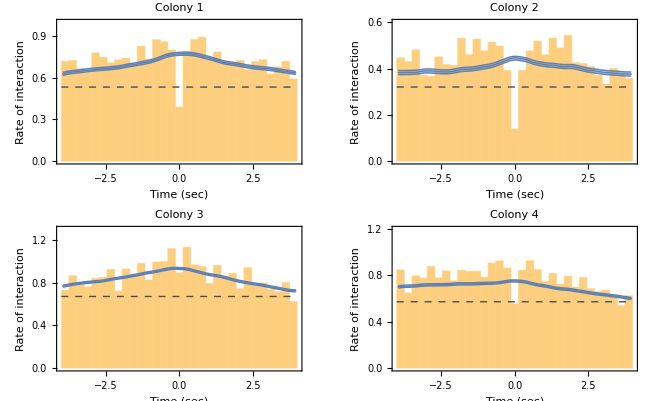

```mathematica
colymax={1,0.6,1.3,1.2};  (* y-max for display *)
togethererror=Table[Show[coldatahists[[col]],colavgplots[[col]],colerrorplots[[col]],colequivplots[[col]],FrameLabel->(Style[#,14]&/@{"Time (sec)","Rate of interaction"}),FrameTicksStyle->14,PlotRange->{Automatic,{0,colymax[[col]]}}],{col,4}];
dispplots=GraphicsGrid[Partition[togethererror,2],ImageSize->650]
```

# Fig 7: Returning and Potential forager data

```mathematica
(* Import density functions, calculated from file (2) *)
densityRF=Get[savedir<>"densityRF"];
densityPF=Get[savedir<>"densityPF"];
```

### Speed comparison: p-values with permutation test

```mathematica
evalfn=Mean;
numtimes=100000;
speedpvalues=Monitor[Table[Module[{data},
data=Table[Mean[Rest@#]&/@Select[allspeeds[[col,group]],Length[#]>0&],{group,4}];
permtest[{Flatten[Take[data,2]],Flatten[Take[data,-2]]},evalfn,numtimes]
],{col,4}],{col}];
TableForm[{speedpvalues}ᵀ,TableHeadings->{colnames,{"p-value"}}]
```

| p-value
colony 1 | 0.04539
colony 2 | 0.11955
colony 3 | 0.1268
colony 4 | 0.04535

### Density differences: p-values with permutation test

```mathematica
(* constant for converting units of density *)
normconst=antsizes^2(Pi (mult antsizes)^2(gweights[[1]]+3gweights[[2]]+5gweights[[3]]))^-1; 

normRFdensity=normconst densityRF;
normPFdensity=normconst densityPF;

normdensitydiff=normRFdensity[[;;,1;;4]]-normPFdensity[[;;,1;;4]];
evalfn=Mean;
numtimes=100000;
densityDIFFpvalues=Monitor[Table[Module[{data},
data=Table[Mean/@Select[normdensitydiff[[col,group]],Length[#]>0&],{group,4}];
permtest[{Flatten[Take[data,2]],Flatten[Take[data,-2]]},evalfn,numtimes]
],{col,4}],{col}];
TableForm[{densityDIFFpvalues}ᵀ,TableHeadings->{colnames,{"p-value"}}]
```

| p-value
colony 1 | 0.00601
colony 2 | 0.79756
colony 3 | 0.0077
colony 4 | 0.

### Box-Whisker plots for speed (left column) and density difference (right column)

```mathematica
ar=1; (* aspect ratio for plots *)
padding={{40,5},{5,5}};
makechartind[data_]:=BoxWhiskerChart[Reverse@data,"Diamond",AspectRatio->ar,ImagePadding->padding,ImageSize->125,ChartStyle->{Red,Blue},LabelStyle->13];
img=Grid[Table[{
makechartind[(Flatten/@Partition[#,2])&@Map[Mean,allspeeds[[col,1;;4]],{2}]],
makechartind[(Flatten/@Partition[#,2])&@Map[Mean,normRFdensity[[col,1;;4]]-normPFdensity[[col,1;;4]],{2}]]
},{col,4}]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Trajectory images for returning foragers (left column) and potential foragers (right column)

```mathematica
RPopacities=90.0/Map[Sqrt[Length[Flatten[#]]]&,{Join@@(#[[1;;2]]),Join@@(#[[3;;4]])}&/@alltrajcoords,{2}];(* for opacities of the trajectories *)
RPtrajimgs=Table[Show[edgeimgnone,edgeimg[[col]],ListPlot[Flatten[alltrajcoords[[col,1+cats;;2+cats]],1],Joined->True,PlotStyle->{{Thickness[.007],Opacity[RPopacities[[col,If[cats==2,2,1]]]],If[cats==2,cfuncR[1],cfuncP[1]]}},Frame->True,FrameTicks->False,PlotRange->{{0,xmax},{0,ymax}}],AspectRatio->ymax/xmax],{col,4},{cats,{2,0}}];
GraphicsGrid[RPtrajimgs,ImageSize->700]
```

-Graphics-

# Fig 8: Correlated random walk model, for returning and potential foragers

Statistics

```mathematica
(* read in the saved data structures, from running "(3) Correlated random walk model" *)
simdensityRF=Get[savedir<>"simdensityRF"];
simdensityPF=Get[savedir<>"simdensityPF"];
```

### Density differences: p-values with permutation test

```mathematica
(* constant for converting units of density *)
normconst=antsizes^2(Pi (mult antsizes)^2(gweights[[1]]+3gweights[[2]]+5gweights[[3]]))^-1; 

normRFsimdensity=normconst simdensityRF;
normPFsimdensity=normconst simdensityPF;

normdensitydiff=normRFsimdensity[[;;,1;;4]]-normPFsimdensity[[;;,1;;4]];
evalfn=Mean;
numtimes=10000;
densityDIFFpvalues=Monitor[Table[Module[{data},
data=Table[Mean/@Select[normdensitydiff[[col,group]],Length[#]>0&],{group,4}];
permtest[{Flatten[Take[data,2]],Flatten[Take[data,-2]]},evalfn,numtimes]
],{col,4}],{col}];
TableForm[{densityDIFFpvalues}ᵀ,TableHeadings->{colnames,{"p-value"}}]
```

| p-value
colony 1 | 0.
colony 2 | 0.
colony 3 | 0.
colony 4 | 0.

### Box-Whisker plots for simulated density difference

```mathematica
ar=1;
padding={{40,5},{5,5}};
makechartind[data_]:=BoxWhiskerChart[Reverse@data,"Diamond",AspectRatio->ar,ImagePadding->padding,ImageSize->125,ChartStyle->{Red,Blue},LabelStyle->13];
img=Grid[Table[{
makechartind[(Flatten/@Partition[#,2])&@Map[Mean[Flatten@#]&,normRFsimdensity[[col,1;;4]]-normPFsimdensity[[col,1;;4]],{2}]]
},{col,4}]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

Generate and view sample simulated trajectories

```mathematica
numcases=1;  (* set to just 1, for displaying here *)
allsimtraj=Monitor[Table[
Table[
boundary=smoothedgedata[[col]];
speedavg=Mean[allspeeds[[col,group,ant]]]*antsizes[[col]];
dt=alldtused[[col]];
PTWant[alltrajcoords[[col,group,ant]],alltimes[[col,group,ant]],speedavg,turnspeeddecayrate,turnspeedsigma,{xmax,ymax},boundary,dt],
numcases],
{col,4},{group,4},{ant,Length[alltimes[[col,group]]]}]
,{col,group,ant}];
```

```mathematica
RPopacities=90.0/Map[Sqrt[Length[Flatten[#]]]&,{Join@@(#[[1;;2]]),Join@@(#[[3;;4]])}&/@alltrajcoords,{2}]  (* for opacities of the trajectories *)
case=1;
RPtrajimgs=Table[Show[edgeimgnone,edgeimg[[col]],ListPlot[Flatten[allsimtraj[[col,1+cats;;2+cats,;;,case]],1],Joined->True,PlotStyle->{{Thickness[.007],Opacity[RPopacities[[col,If[cats==2,2,1]]]],If[cats==2,cfuncR[1],cfuncP[1]]}},Frame->True,FrameTicks->False,PlotRange->{{0,xmax},{0,ymax}}],AspectRatio->ymax/xmax],{col,4},{cats,{2,0}}];
GraphicsGrid[RPtrajimgs,ImageSize->700]
```

{{0.303569,0.373242},{0.317169,0.361076},{0.339104,0.364143},{0.214455,0.27857}}

-Graphics-

# Fig 5, Fig 9: Collision theory

Define models

```mathematica
(* import calculations from "(2) Density and collision theory calculations"*)
(* for random mixture model *)
randmixcountsRF=Get[savedir<>"randmixcountsRF"];
avgspeedRF=Get[savedir<>"avgspeedRF"];

(* for local density model *)
densityRF=Get[savedir<>"densityRF"]; (* density of returning foragers, surrounding each focus ant *)
relativeRFspeeddensity=Get[savedir<>"relativeRFspeeddensity"];
```

```mathematica
allNactualRF=Map[Length,allintsRF,{3}]; (* actual counts of interactions with returning foragers *)
allspeedsmodelcalcs=Map[getspeed[#,smfactor]&,alltrajcoords,{3}]; (* use non-normalized speed for these calculations *)
randmixprobsRF=Sqrt[allspeedsmodelcalcs^2+avgspeedRF^2]*randmixcountsRF; (* random mixture model *)
localdensityprobsRF=Sqrt[(allspeedsmodelcalcs*densityRF)^2+relativeRFspeeddensity^2];
models={randmixprobsRF,localdensityprobsRF};

integrated=Map[integrateprob[#,1]&,#,{3}]&/@models;  
totals=getTotalIntegrated/@integrated; (* partition function*)
totalinteractionsRF=ConstantArray[Total[Flatten[#]]&/@allNactualRF,Length@models];
normprobs=1/totals(models*totalinteractionsRF);  (* normalized probabilities *)
avgN=Map[integrateprob[#,1]&,normprobs,{4}]; (* model predictions for the average number of interactions that each ant makes with returning foragers *)
```

Fig 5:  Illustrative plot, probability functions

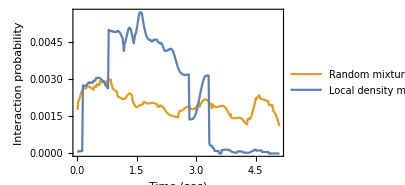

```mathematica
tpall=normprobs[[;;,4,1,101]];
tptime=Range[Length[tpall[[1]]]]*1.0/60;
plot1=ListPlot[{tptime,#}ᵀ&/@tpall,Joined->True,PlotStyle->{colors[[2]],colors[[1]]},PlotLegends->(Style[#,14]&/@{"Random mixture model:\nN^RFP_(mix,i)(t)","Local density model:\nN^RFP_(LD,i)(t)"}),ImageSize->300,Frame->True,FrameTicksStyle->12,FrameLabel->(Style[#,14]&/@{"Time (sec)","Interaction probability"}),PlotRange->{Automatic,{0,Automatic}}]
```

Fig 9C:  Correlation

### Correlation

```mathematica
dispcolors={colors[[2]],colors[[1]],colors[[3]],colors[[4]]};
modelnames={"Random mixture","Local density"}
plots=Table[Module[{data},
data=Table[Flatten[Table[{allNactualRF[[col,group]]/alltimes[[col,group]],avgN[[mod,col,group]]/alltimes[[col,group]]}ᵀ,{group,2}],1],{col,4}];
Show[
ListPlot[
data,PlotStyle->{dispcolors,ConstantArray[PointSize[.015],4],ConstantArray[Opacity[0.7],4]}ᵀ,
PlotRange->{{-0.025,1.0},{-0.025,1.0}},PlotLabel->Style[(modelnames[[mod]]<>" model\nCorrelation = "<>ToString[Correlation@@(Flatten[data,1]ᵀ)])],Frame->True,FrameLabel->({"Observed rate of interaction\nwith returning foragers","Avg. model prediction"}),LabelStyle->15],
Plot[x,{x,0,3},PlotStyle->{{Gray,Dashed}}],ImageSize->400]
]
,{mod,2}
];
corrplots=GraphicsRow[Append[plots,
Show[Plot[x,{x,0,1},ImageSize->0,PlotLegends->PointLegend[dispcolors,Style["Colony "<>ToString[#],16,TextAlignment->Left]&/@Range[4]]]]
]]
```

{Random mixture,Local density}

-Graphics-

Fig 9A-B:  Collision theory model

### Calculate distributions of possible numbers of interactions, using simulations with the probability functions (Note: this takes a few minutes to run)

```mathematica
numruns=5000;
(* the function getNvalues does the simulation using the probability functions *)
distN=Monitor[Table[Table[getNvalues[normprobs[[mod,col,group,ant]],numruns],{col,4},{group,2},{ant,Length[allNactualRF[[col,group]]]}],{mod,1,2}],{mod,col,group}];
```

### Fig 9A: Plots of mean interaction rate of potential foragers with returning foragers, using each model

3

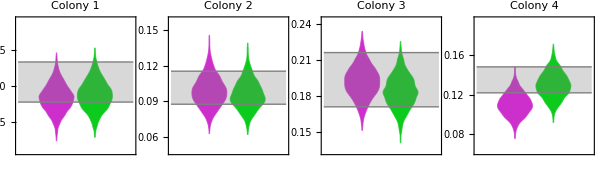

```mathematica
Needs["ErrorBarPlots`"];
yranges={0.85,0.7,0.9,1};
mid=3
max=5.5;
plots=Table[
datadists=allNactualRF[[col,1;;2]]/alltimes[[col,1;;2]];
meandiff=Mean[Join[datadists[[1]],datadists[[2]]]];
sediff=Sqrt[Variance[Join[datadists[[1]],datadists[[2]]]]/Length[Join[datadists[[1]],datadists[[2]]]]];
modeldists=Table[Table[Mean[Join[distN[[mod,col,1,;;,q]]/alltimes[[col,1]],distN[[mod,col,2,;;,q]]/alltimes[[col,2]]]],{q,numruns}],{mod,2}];
Show[
DistributionChart[modeldists,BarSpacing->{0.1,1},ChartStyle->{{cfuncleave[0.65],cfuncreturn[0.65]}},AxesOrigin->0,Axes->True,PlotRange->{Automatic,{0,Automatic}}],
Plot[{meandiff+sediff,meandiff-sediff},{x,0,3},Filling->{1->{2}},PlotStyle->{{Gray,Opacity[1],Thin}},FillingStyle->Opacity[0.3]],
PlotLabel->Style["Colony "<> ToString[col],16],PlotRange->Automatic,ImageSize->350, FrameTicksStyle->14,AspectRatio->1.2]
,{col,4}];
img=GraphicsRow[plots,ImageSize->600]
```

### Fig 9B: Difference in interaction rate: PF-leave - PF-return

3

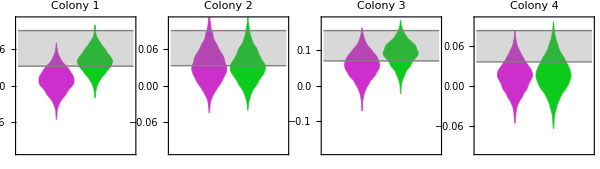

```mathematica
Needs["ErrorBarPlots`"];
yranges={0.85,0.7,0.9,1};
mid=3
max=5.5;
plots=Table[
datadists=allNactualRF[[col,1;;2]]/alltimes[[col,1;;2]];
meandiff=Mean[datadists[[1]]]-Mean[datadists[[2]]];
sediff=Sqrt[Variance[datadists[[1]]]/Length[datadists[[1]]]+Variance[datadists[[2]]]/Length[datadists[[2]]]];
modeldists=Table[Table[Mean[distN[[mod,col,1,;;,q]]/alltimes[[col,1]]]-Mean[distN[[mod,col,2,;;,q]]/alltimes[[col,2]]],{q,numruns}],{mod,2}];
plotSym[Show[
DistributionChart[modeldists,BarSpacing->{0.1,1},ChartStyle->{{cfuncleave[0.65],cfuncreturn[0.65]}},AxesOrigin->0,Axes->True],
Plot[{meandiff+sediff,meandiff-sediff},{x,0,3},Filling->{1->{2}},PlotStyle->{{Gray,Opacity[1],Thin}},FillingStyle->Opacity[0.3]],
PlotLabel->Style["Colony "<> ToString[col],16],PlotRange->Automatic,ImageSize->350, FrameTicksStyle->14,AspectRatio->1.2]]
,{col,4}];
img=GraphicsRow[plots,ImageSize->600]
```

# Fig 10: Potential forager comparison: PF-leave, PF-return

```mathematica
(* Import density function, calculated from file (2) *)
densityRF=Get[savedir<>"densityRF"];
```

### Speed comparison: p-values with permutation test

```mathematica
evalfn=Mean;
numtimes=100000;
speedpvalues=Monitor[Table[Module[{data},
data=Table[Mean[Rest@#]&/@Select[allspeeds[[col,group]],Length[#]>0&],{group,2}];
permtest[data,evalfn,numtimes]
],{col,4}],{col}];
TableForm[{speedpvalues}ᵀ,TableHeadings->{colnames,{"p-value"}}]
```

| p-value
colony 1 | 0.00547
colony 2 | 0.00036
colony 3 | 0.
colony 4 | 0.

### Density differences: p-values with permutation test

```mathematica
(* constant for converting units of density *)
normconst=antsizes^2(Pi (mult antsizes)^2(gweights[[1]]+3gweights[[2]]+5gweights[[3]]))^-1; 
normRFdensity=normconst densityRF;

evalfn=Mean@Flatten@#&;
numtimes=100000;
densitypvalues=Monitor[Table[Module[{data},
data=Table[Mean/@Select[normRFdensity[[col,group]],Length[#]>0&],{group,2}];
permtest[data,evalfn,numtimes]
],{col,4}],{col}];
TableForm[{densitypvalues}ᵀ,TableHeadings->{colnames,{"p-value"}}]
```

| p-value
colony 1 | 0.36782
colony 2 | 0.94437
colony 3 | 0.36766
colony 4 | 0.47577

### Box-Whisker plots for speed (left column) and density difference (right column)

```mathematica
ar=1; (* aspect ratio *)
padding={{40,5},{5,5}};
makechartind[data_]:=BoxWhiskerChart[data,"Diamond",AspectRatio->ar,ImagePadding->padding,ImageSize->125,ChartStyle->{cfuncleave[0.65],cfuncreturn[0.65]},LabelStyle->13];
img=Grid[Table[{
makechartind[Map[Mean,allspeeds[[col,1;;2]],{2}]],
makechartind[Map[Mean,normRFdensity[[col,1;;2]],{2}]]
},{col,4}]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Trajectory images for Potential foragers that left to nest to forager (left column) and Potential foragers that returned to the deeper nest (right column)

```mathematica
LRdarkness=0.85;
cat2opacities=90.0/Map[Sqrt[Length[Flatten[#]]]&,Take[#,2]&/@alltrajcoords,{2}];  (* for opacities of the trajectories *)
cat2trajimgs=Table[Show[edgeimgnone,edgeimg[[col]],ListPlot[Flatten[alltrajcoords[[col,group]],0],Joined->True,PlotStyle->{{Thickness[.007],Opacity[cat2opacities[[col,group]]],If[group==1,cfuncleave[LRdarkness],cfuncreturn[LRdarkness]]}},Frame->True,FrameTicks->False,PlotRange->{{0,xmax},{0,ymax}}],AspectRatio->ymax/xmax],{col,4},{group,2}];
GraphicsGrid[cat2trajimgs,ImageSize->700]
```

-Graphics-